/Users/derekostrom/Desktop/MCFromFSL/MonteCarlo/10/10000000

{180.}

/Users/derekostrom/Desktop/MCFromFSL/MonteCarlo/4/10000000

{180.}

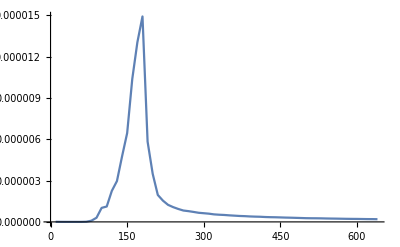

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["MonteCarlo/10/10000000/"]
file = Drop[Import["MCsimanneal.out","Table"],9];
x=file⟦All,2⟧;
y=file⟦All,4⟧;
maxnum=Max[y];
pos=Position[y,maxnum];
x⟦Flatten[pos]⟧
data=Transpose@{x,y};
SetDirectory[NotebookDirectory[]];
SetDirectory["MonteCarlo/4/10000000/"]
file2= Drop[Import["MCsimanneal.out","Table"],9];
x2=file2⟦All,2⟧;
y2=file2⟦All,4⟧/10;
maxnum=Max[y];
pos=Position[y,maxnum];
x⟦Flatten[pos]⟧
data2=Transpose@{x2,y2};
graphs=ListPlot[data,PlotRange->All,TicksStyle->Directive[FontSize->18],Joined->True]
Export["SpecificHeat.png",graphs];
```